```mathematica
x[t]=(l/2)*Cos[θ[t]]
```

1/2 l Cos[θ[t]]

```mathematica
D[D[x[t],t],t]//FullSimplify
```

-1/2 l (Cos[θ[t]] θ'[t]^2+Sin[θ[t]] θ''[t])

```mathematica
y[t]=(l/2)*Sin[θ[t]]
```

1/2 l Sin[θ[t]]

```mathematica
D[D[y[t],t],t]//FullSimplify
```

1/2 (-l Sin[θ[t]] θ'[t]^2+l Cos[θ[t]] θ''[t])

```mathematica
Solve[m*D[D[x[t],t],t]==λ1,λ1][[1]]
```

{λ1→-1/2 m (l Cos[θ[t]] θ'[t]^2+l Sin[θ[t]] θ''[t])}

```mathematica
Solve[m*D[D[y[t],t],t]+m*g==λ2,λ2][[1]]
```

{λ2→1/2 (2 g m-l m Sin[θ[t]] θ'[t]^2+l m Cos[θ[t]] θ''[t])}

```mathematica
λ1=-1/2 m (l Cos[θ[t]] θ'[t]^2+l Sin[θ[t]] θ''[t])
```

-1/2 m (l Cos[θ[t]] θ'[t]^2+l Sin[θ[t]] θ''[t])

```mathematica
λ2=1/2 (2 g m-l m Sin[θ[t]] θ'[t]^2+l m Cos[θ[t]] θ''[t])
```

1/2 (2 g m-l m Sin[θ[t]] θ'[t]^2+l m Cos[θ[t]] θ''[t])

```mathematica
Solve[FullSimplify[θ''[t]*m*l^2/12==λ1*(l/2)*Sin[θ[t]]-λ2*(l/2)*Cos[θ[t]]],θ''[t]]
```

{{θ''[t]→-(3 g Cos[θ[t]])/(2 l)}}

```mathematica
Integrate[1/Sqrt[Sin[T]-Sin[T0]],T]
```

-(2 EllipticF[1/4 (π-2 T),-2/(-1+Sin[T0])] √((-Sin[T]+Sin[T0])/(-1+Sin[T0])))/(√(Sin[T]-Sin[T0]))

```mathematica
Solve[θ''[t]*l^2/12==(l/2)*(-Sin[θ[t]]/2 (l Cos[θ[t]] θ'[t]^2+l Sin[θ[t]] θ''[t])+Cos[θ[t]]/2 (2 g +l  Sin[θ[t]] θ'[t]^2-l  Cos[θ[t]] θ''[t])),θ''[t]]
```

{{θ''[t]→(0.+14.7 Cos[θ[t]])/(0.75+2.25 Cos[θ[t]]^2+2.25 Sin[θ[t]]^2)}}

```mathematica
tEnd=Re[Integrate[-1/Sqrt[-3*9.8/3*(Sin[Theta]-Sin[Pi/3])],{Theta,Pi/3,ArcSin[(2/3)*Sin[Pi/3]]}]]
```

0.563257

```mathematica
l=3;
g=-9.8;
```

```mathematica
s=NDSolve[{x''[t]==-1/2 (l Cos[θ[t]] θ'[t]^2+l Sin[θ[t]] θ''[t]),
y''[t]-g==-1/2 (2 g +l  Sin[θ[t]] θ'[t]^2-l  Cos[θ[t]] θ''[t]),
θ''[t]*l^2/12==(l/2)*(-l*Sin[θ[t]]/2 (l Cos[θ[t]] θ'[t]^2+l Sin[θ[t]] θ''[t])+l*Cos[θ[t]]/2 (2 g +l  Sin[θ[t]] θ'[t]^2-l  Cos[θ[t]] θ''[t])),
θ[0]==Pi/3,
x[0]==(l/2)*Cos[Pi/3],
y[0]==(l/2)*Sin[Pi/3],
θ'[0]==0,
x'[0]==0,
y'[0]==0},
{x,y,θ},{t,0,tEnd}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…],θ→InterpolatingFunction[…]}}

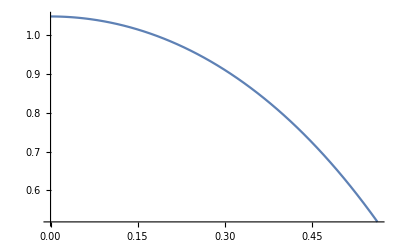

```mathematica
Plot[Evaluate[θ[t]/. s],{t,0,tEnd},PlotRange->All]
```

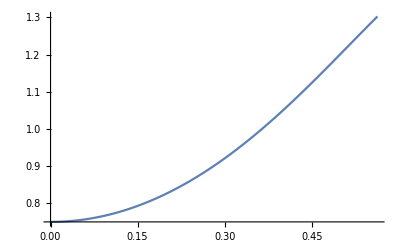

```mathematica
Plot[Evaluate[x[t]/. s],{t,0,tEnd},PlotRange->All]
```

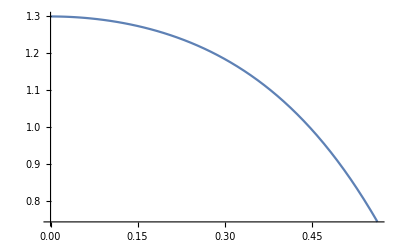

```mathematica
Plot[Evaluate[y[t]/. s],{t,0,tEnd},PlotRange->All]
```

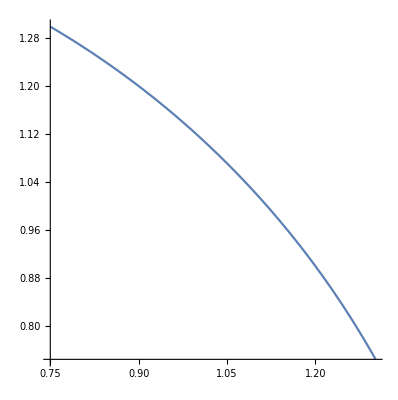

```mathematica
ParametricPlot[Evaluate[{x[t],y[t]}/.s],{t,0,tEnd},PlotRange->All]
```

```mathematica
Evaluate[{x'[t],y'[t],θ'[t]}/.s]/.{t->tEnd}
```

{{1.55215,-2.71623,-2.08562}}

```mathematica
Evaluate[{x[t],y[t],θ[t]}/.s]/.{t->tEnd}
```

{{1.30236,0.744217,0.519152}}

```mathematica
s1=NDSolve[{x''[t]==0,
y''[t]-g==-1/2 (2 g +l  Sin[θ[t]] θ'[t]^2-l  Cos[θ[t]] θ''[t]),
θ''[t]*l^2/12==(l/2)*(0+l*Cos[θ[t]]/2 (2 g +l  Sin[θ[t]] θ'[t]^2-l  Cos[θ[t]] θ''[t])),
θ[tEnd]==0.5191523437896627,
x[tEnd]==1.3023600477763517,
y[tEnd]==0.7442165221608971,
θ'[tEnd]==-2.085617584046668,
x'[tEnd]==1.5521510608501383,
y'[tEnd]==-2.716225073614928},
{x,y,θ},{t,tEnd,1}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…],θ→InterpolatingFunction[…]}}

```mathematica
(*Need to stop when Theta = 0. What is t for which Theta = 0?*)
```

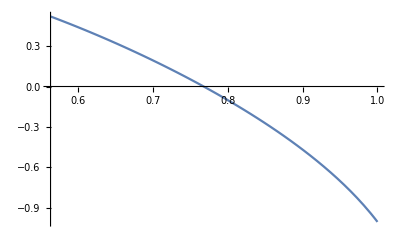

```mathematica
Plot[Evaluate[θ[t]/. s1],{t,tEnd,1},PlotRange->All]
```

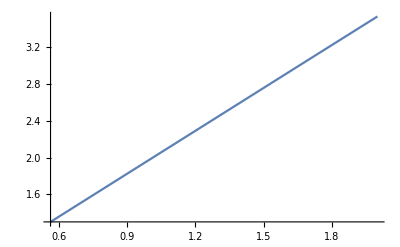

```mathematica
Plot[Evaluate[x[t]/. s1],{t,tEnd,2},PlotRange->All]
```

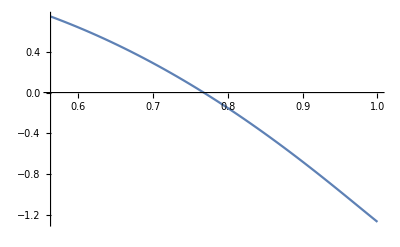

```mathematica
Plot[Evaluate[y[t]/. s1],{t,tEnd,1},PlotRange->All]
```